# Thesis Notebook

## 2D Orbit with the Tolman VII neutron star density profile and mass function, along with dissipative forces

## Setting functions up and choosing variables

```mathematica
(*R values in Schwarzschild coordinates*)
RStar = 8;(*Radius of the Star*)
M = 1;
```

## Exterior Schwarzschild Isotropic coordinates definitions r(r̄), r̄(r), A(r̄), α(r̄)

### r(r̄), r̄(r)

```mathematica
rofrbarOutside[rbar_] :=rbar (1 + M/(2 rbar))^2; 

rbarofrOutside[r_] := 1/2 (-M + r + Sqrt[r^2 - 2 M r]);
```

### Shift, Lapse and rbarStar

```mathematica
A[rbar_] :=(1 + M/(2 rbar))^2;
α[rbar_] :=(1 - M/(2 rbar))/(1 + M/(2 rbar));
```

```mathematica
rbarStar = rbarofrOutside[RStar] //  N
```

6.9641

## Tolman VII Isotropic coords definitions

### Constants

```mathematica
ScriptC = M/RStar;
```

### Universal alpha factor

```mathematica
(*alpha:=a0+a1*(Cn/(rhoc*R^2))+a2*(Cn/(rhoc*R^2))^2*)
alphaaa=3.70625 -1.50266*(ScriptC^(.903)/(rho0*RStar^2))+0.0643875*(ScriptC^(.903)/(rho0*RStar^2))^2 ;
(*alphaaa = 1*)
```

### New interior rho

```mathematica
rho[r_] := rho0(1 - alphaaa (r/RStar)^2 + (alphaaa-1)(r/RStar)^4)
```

```mathematica
massIntegral =  4 Pi Integrate[rho[r] r^2, {r, 0, RStar}]
```

4 π (0.105056-0.000010757/rho0-10.9105 rho0)

```mathematica
sol = NSolve[massIntegral == 1, rho0]
```

{{rho0→0.00178199},{rho0→0.000553279}}

```mathematica
rho0 = rho0 /. sol[[1]] (*Larger density seems more realistic for neutron star*)
```

0.00178199

```mathematica
massIntegral =  4 Pi Integrate[rho[r] r^2, {r, 0, RStar}]
```

1.

### New mass function

```mathematica
MassFunc[r_] := Piecewise[
{
{4 Pi rho0 RStar^3 ( 1/3(r/RStar)^3 - alphaaa/5(r/RStar)^5 + ((alphaaa-1)/7)(r/RStar)^7), r < RStar},
{M, r >= RStar}
}
]
```

### Need old grr is continuous

```mathematica
grrTolPowerMinOne[r_] := (1 - ScriptC (r/RStar)^2(5 - 3(r/RStar)^2))
grrTolPowerMinOne[RStar]
```

3/4

## Numerically integrating for the pressure and the phi in α = exp(phi)

### Defining the ODEs

```mathematica
(*TOV differential equation*)
dPdr[r_, Pressure_] := -(rho[r] + Pressure)((MassFunc[r] + 4 Pi Pressure r^3)/(r(r-2MassFunc[r])));
```

```mathematica
(*Phi differential equation for metric*)
dPhidrMetric[r_, Pressure_] := ((MassFunc[r] + 4 Pi Pressure r^3)/(r(r-2MassFunc[r])));
```

#### Numerically integrating these coupled ODEs

```mathematica
rmin = 10^-16 (*For these integrations*);
```

```mathematica
eq1 = P'[r] == dPdr[r, P[r]];
eq2 = Phi'[r] == dPhidrMetric[r, P[r]];
BCs = {P[RStar] == 0, Phi[RStar] == 1/2 Log[1-2 M/RStar]} ;(*Phi[RStar] from the Schwarzschild metric*)
```

```mathematica
sol1 = NDSolve[
{eq1,
eq2,
BCs},
{P, Phi},
{r, RStar, 0}
][[1]]; (*Very small rmin to avoid singularity sarp mentioned*)
```

```mathematica
Pressure[r_] := P[r] /. sol1

PhiMetric[r_] = Phi[r] /. sol1;

(*Plot[Derivative[1][PhiMetric][r], {r, 0, RStar}]*)
(*Causing the issue it seems, but we have this Analytically!*)
```

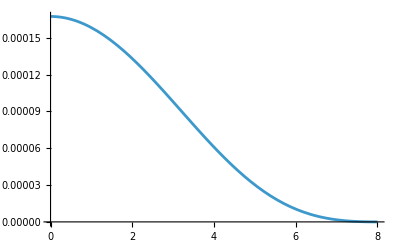

```mathematica
Plot[Pressure[r], {r, 0, RStar}, PlotRange->All]
```

## Solving for r̄(r) and r(r̄) inside

### Defining the ODE

```mathematica
drbardr[rbar_, r_] := rbar/r(1 - (2MassFunc[r])/r)^(-1/2)
```

### Numerically Integrating the above equation

```mathematica
eq = rbarofr'[r] == drbardr[rbarofr[r], r];
BC = {rbarofr[RStar] == rbarStar};
```

```mathematica
sol2 = NDSolve[
{eq,
BC},
{rbarofr},
{r, RStar, rmin}
(*WorkingPrecision->40,
AccuracyGoal->20, (*I want the answer correct up to 10^-8 -> 8 correct decimals*)
PrecisionGoal->20*) (*I want 8 correct digits relative to the size of the number. E.g if answer is 1.234567899, then precision goal gives me say 1.23456789 - the amount of digits is 8 and accuracy goal makes these 8 digits exact.*)
][[1]];
```

```mathematica
rbarofrInside[r_] = rbarofr[r] /. sol2;
```

#### Some sanity checks

```mathematica
rbarofrInside[RStar]
rbarofrOutside[RStar] //N
```

6.9641

6.9641

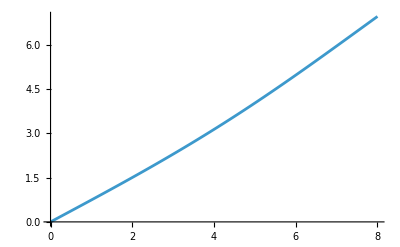

```mathematica
Plot[rbarofrInside[r], {r, 0, RStar}]
```

### Now using the interpolation trick to obtain r(r̄):

```mathematica
(*Table[ expression, {variable, start, end, step}*)
data = Prepend[Table[
{rbarofrInside[r], r}, 
{r, rmin, RStar, (RStar - rmin)/100000} (*10000 points and A is not messy*)
], {0,0}];
```

```mathematica
rofrbarInside = Interpolation[data];
```

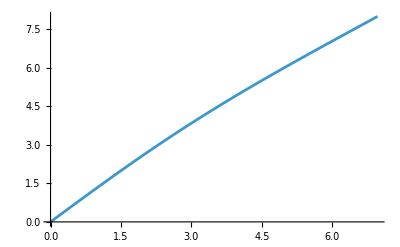

```mathematica
Plot[rofrbarInside[rbar], {rbar, 0, rbarStar}]
```

## Finding the interior metric functions

### Getting αInside(r̄):

```mathematica
αInside[rbar_?NumericQ] := Exp[PhiMetric[rofrbarInside[rbar]]]
```

#### Sanity checks

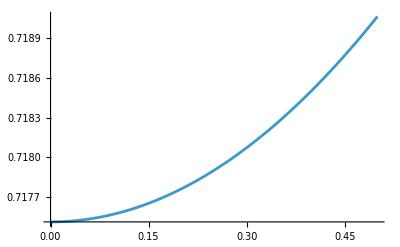

```mathematica
Plot[αInside[rbar], {rbar, 0, .5}]
```

```mathematica
αInside[rbarStar]
α[rbarStar]
```

0.866025

0.866025

```mathematica
αFull[rbar_] := Piecewise[
{
{αInside[rbar], rbar < rbarStar},
{α[rbar], rbar >= rbarStar}
}
]
(*αFull[rbar_]:=If[rbar<rbarStar,αInside[rbar],α[rbar]]*)
```

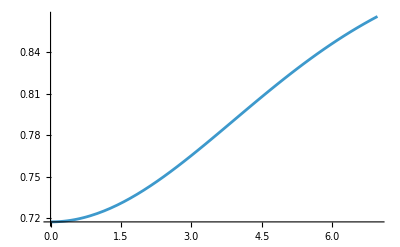

```mathematica
Plot[αFull[rbar], {rbar, 0, rbarStar}]
```

### Making the derivative of alpha continuous

#### Interior derivative in terms of r

Doing things in r first as this is more analytic

```mathematica
dPhidrMetric[r_] := ((MassFunc[r] + 4 Pi Pressure[r] r^3)/(r(r-2MassFunc[r])))
```

```mathematica
alpha[r_] := Exp[PhiMetric[r]]
DERalphaIns[r_] := dPhidrMetric[r] alpha[r] (*Analytic times numerical integral*)
```

Exterior derivative

```mathematica
DERαOutsiderbardummy = Derivative[1][α][rbar];
DERαOutsiderbar[r_] := ((1-1/(2 rbar))/(2 (1+1/(2 rbar))^2 rbar^2)+1/(2 (1+1/(2 rbar)) rbar^2) )/. rbar -> rbarofrOutside[r] (*More accurate subbing in after for rbar maybe?*)
drbardr[r_] := rbarofrOutside[r]/r(1 - (2MassFunc[r])/r)^(-1/2)
```

```mathematica
DERalpha[r_] := drbardr[r]  DERαOutsiderbar[r] (*Chain rule*)
```

### Checking to see if it worked

#### Numbers at star boundary

```mathematica
DERalpha[RStar] //N
DERalphaIns[RStar] //N
```

0.0180422

0.0180422

```mathematica
DERalpha[rbarofrOutside[RStar]] //N
DERalphaIns[rbarofrInside[RStar]] //N (*More or less continuous now but not exact*)
```

0.024182

0.0229633

```mathematica
diff = Abs[1 - DERalphaIns[rbarofrInside[RStar]]/DERalpha[rbarofrOutside[RStar]]]
```

0.0503996

```mathematica
Abs[Log10[diff]] (*Amount of digits in agreement*)
```

1.29757

#### Plots at star boundary

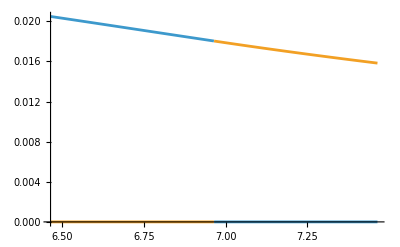

```mathematica
Plot[{Piecewise[{{DERalphaIns[rofrbarInside[rbar]],rbar<=rbarStar}}],Piecewise[{{DERalpha[rofrbarOutside[rbar]],rbar>=rbarStar}}]},{rbar,rbarStar-0.5,rbarStar+0.5}]
```

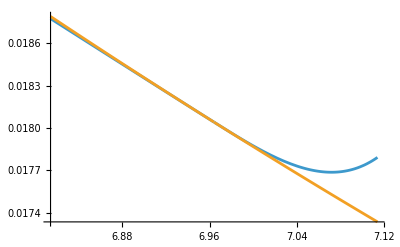

```mathematica
Plot[{DERalphaIns[rofrbarInside[rbar]],DERalpha[rofrbarOutside[rbar]]},{rbar,rbarStar-0.15,rbarStar+0.15}]
```

### Proper definitions in isotropic coords now

```mathematica
DERαOutside[rbar_] := Module[{r = rofrbarOutside[rbar]}, drbardr[r]  DERαOutsiderbar[r]]

DERαInside[rbar_] := Module[{r = rofrbarInside[rbar]},
dPhidrMetric[r] alpha[r]]
```

```mathematica
DERαFull[rbar_] := Piecewise[
{
{DERαInside[rbar], rbar < rbarStar},
{DERαOutside[rbar], rbar >= rbarStar}
}
]
```

```mathematica
DERαInside[rbarStar]
```

0.0180422

```mathematica
DERαOutside[rbarStar]
```

0.0180422

```mathematica
(*DERαFull[rbar_]:=If[rbar<rbarStar,DERαInside[rbar],DERαOutside[rbar]]*)
```

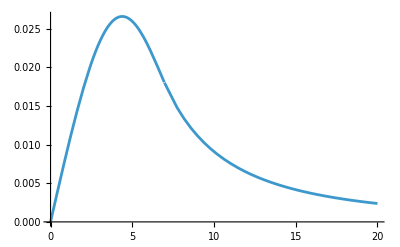

```mathematica
Plot[DERαFull[rbar], {rbar, 0, 20}]
```

Going to do the same derivative setup as the α component for the A component

```mathematica
AInside[rbar_?NumericQ] := rofrbarInside[rbar]/rbar;
```

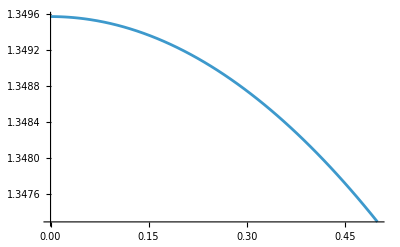

```mathematica
Plot[AInside[rbar], {rbar, 0, .5}]
```

```mathematica
A[rbarStar]
AInside[rbarStar]
```

1.14875

1.14875

```mathematica
AFull[rbar_] := Piecewise[
{
{A[rbar], rbar >= rbarStar},
{AInside[rbar], rbar < rbarStar}
}
];
(*AFull[rbar_]:=If[rbar<rbarStar,AInside[rbar],A[rbar]]*)
```

```mathematica
drbardr[rbar_, r_] := rbar/r(1 - (2MassFunc[r])/r)^(-1/2)
drdrbar[rbar_] := rofrbarInside[rbar]/rbar(1 - (2MassFunc[rofrbarInside[rbar]])/rofrbarInside[rbar])^(1/2)
```

```mathematica
DERAInside[rbar_] := drdrbar[rbar]/rbar - rofrbarInside[rbar]/rbar^2;
DERAOutside[rbar_] := Derivative[1][A][rbar]
```

```mathematica
DERAFull[rbar_] := Piecewise[
{
{DERAOutside[rbar], rbar >=rbarStar},
{DERAInside[rbar], rbar < rbarStar}
}
];
(*DERAFull[rbar_]:=If[rbar<rbarStar,DERAInside[rbar],DERAOutside[rbar]]*)
```

```mathematica
DERAOutside[rbarStar]
DERAInside[rbarStar]
```

-0.0220995

-0.0220995

```mathematica
drhodr[r_]:= Derivative[1][rho][r]
```

```mathematica
IsotropicCoordsPressure[rbar_] := Pressure[rofrbarInside[rbar]]
```

### Sorting out the speed of sound as a function of r: a(r)

#### Speed of sound in isotropic coordinates

```mathematica
(*Needed to implement these measures to speed things up using Module to avoid recomputation and also the N@ to return numbers instead of symbols for NDSolve, pressure was causing an issue*)
(*Module avoids repeating the calculation three times as there were three arguments I would have had to have inputted it in*)
```

```mathematica
asosPiecewise[rbar_?NumericQ]:=Module[{r=rofrbarInside[rbar]},Piecewise[{
{N@Sqrt[dPdr[r,Pressure[r]]/drhodr[r]],rbar<.9999999999rbarStar},
{10^-6, rbar >= .9999999999rbarStar}
}
]
]
```

```mathematica
(*asosPiecewise[rbar_?NumericQ]:=Module[{r=rofrbarInside[rbar]}, N@Sqrt[dPdr[r,Pressure[r]]/drhodr[r]]]*)
```

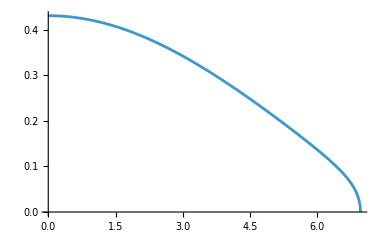

1/1000000

```mathematica
Plot[asosPiecewise[rbar], {rbar, 0, rbarStar}]
asosPiecewise[.9999999999rbarStar]
```

## Setting up 2D ODEs for new density profile:

```mathematica
Isorho[rbar_] := Module[{r = rofrbarInside[rbar]}, rho0(1 - alphaaa (r/RStar)^2 + (alphaaa-1)(r/RStar)^4)]
```

Constants that are going to be used

```mathematica
m = 10^-6; (*mass of PBH?*)
λGR[rbar_] := 1.49*asosPiecewise[rbar]
q = 2;
```

### Mach number interpolation

#### Interpolating

```mathematica
fMachLow[m_] := 1/2 Log[(1+ m)/(1 - m)] - m ;
fMachhigh[m_] := 1/2 Log[1 - 1/m^2]  + 10
```

```mathematica
x1=.98;
x2=1.02;
y1=fMachLow[x1];
y2=fMachhigh[x2];
```

```mathematica
anaylticline[Mach_] := y1 + (y2 - y1) (Mach - x1)/(x2 - x1)
```

```mathematica
IVariableInterpolated[Μach_] := Piecewise[{
{1/2 Log[(1+ Μach)/(1 - Μach)] - Μach, Μach < 0.98},
{anaylticline[Μach], 0.98 < Μach  < 1.02},
{1/2 Log[1 - 1/Μach^2]  + 10, Μach > 1.02}
}];
```

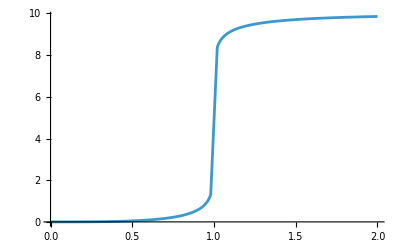

```mathematica
Plot[IVariableInterpolated[Mach], {Mach, 0, 2}, Exclusions->None, PlotRange->All]
```

### Outside Star

#### Velocities

```mathematica
Ut[rbar_, ur_, uphi_] := (√(1 + (ur/A[rbar])^2 + (uphi/(rbar A[rbar]))^2))/α[rbar];
umagOutside[rbar_, ur_, uphi_]:=(√(ur^2+(uphi/rbar)^2))/A[rbar]
```

#### Rates of change of velocities

```mathematica
drBardt[rbar_, ur_, uphi_] := 1/(A[rbar]^2 Ut[rbar, ur, uphi])ur;

dphidtOutside[rbar_,ur_, uphi_] := 1/(rbar^2*A[rbar]^2*Ut[rbar, ur,uphi])uphi;
```

Gravitational Waves

```mathematica
FRRr[m_, rbar_,ur_, uphi_]:=Module[{r = rofrbarOutside[rbar]},((8 m^2)/(15 r^4)*drBardt[rbar, ur, uphi]*(8 M^2+r M (6 drBardt[rbar, ur, uphi]^2+36 r^2 dphidtOutside[rbar,ur, uphi]^2)))];
```

```mathematica
FRRphi[m_, rbar_,ur_, uphi_]:= Module[{r = rofrbarOutside[rbar]},((8 m^2)/(5 r^4)*dphidtOutside[rbar,ur, uphi]*(2 M^2+r M (9 drBardt[rbar, ur, uphi]^2-6 r^2 dphidtOutside[rbar,ur, uphi]^2)))];
```

```mathematica
duphidtOutside[m_, rbar_, ur_, uphi_] := η/m(A[rbar]^2 rbar^2 FRRphi[m, rbar, ur, uphi]);

durdt2DOutside[m_, rbar_, ur_, uphi_] := -α[rbar] Ut[rbar, ur, uphi] DERαOutside[rbar] + ur^2/Ut[rbar, ur, uphi](DERAOutside[rbar]/A[rbar]^3) + uphi^2/Ut[rbar, ur, uphi](1/(rbar^3 *A[rbar]^2) + DERAOutside[rbar]/(rbar^2*A[rbar]^3)) + η/m(A[rbar]^2 FRRr[m, rbar, ur, uphi]);
```

```mathematica
(*η/m(A[rbar]^2 rbar^2 FRRphi[rbar, ur, uphi])
+ η/m(A[rbar]^2 FRRr[rbar, ur, uphi])*)
```

### Inside Star

#### Velocities

```mathematica
UtInside[rbar_, ur_, uphi_] := (√(1 + (ur/AInside[rbar])^2 + (uphi/(rbar AInside[rbar]))^2))/αInside[rbar];
umagInside[rbar_, ur_, uphi_] := (√(ur^2+(uphi/rbar)^2))/AInside[rbar]
```

#### Mach business

```mathematica
Mach[rbar_, ur_, uphi_] :=((√(ur^2+(uphi/rbar)^2))/AInside[rbar])/(asosPiecewise[rbar] αInside[rbar] UtInside[rbar, ur, uphi])
```

#### Dissipative Forces

Accretion

```mathematica
(*q=2, Γ=2*)
(*mdot[m_, rbar_, ur_, uphi_] := 1.49* (4Pi rho0 m^2)/(asosPiecewise[rbar]^2 + (umagInside[rbar, ur, uphi]/(αInside[rbar] UtInside[rbar, ur, uphi]))^2);*)
```

```mathematica
mdot[m_, rbar_, ur_, uphi_] := (4Pi Isorho[rbar] m^2)/((asosPiecewise[rbar]^2 + (umagInside[rbar, ur, uphi]/(αInside[rbar] UtInside[rbar, ur, uphi]))^2)^(3/2)); (*General Bondi-Hoyle-Lyttleton formula for mass accretion with q = 3 and λ=1*)
```

```mathematica
(*dpdtaccretionr[m_, rbar_, ur_, uphi_] := -((4 Pi αInside[rbar] (1.49)(Isorho[rbar] + IsotropicCoordsPressure[rbar])m^2))(1/(asosPiecewise[rbar]^2+(umagInside[rbar, ur, uphi]/(αInside[rbar] UtInside[rbar, ur, uphi]))^2))ur;

dpdtaccretionphi[m_, rbar_, ur_, uphi_] := -((4 Pi αInside[rbar] (1.49)(Isorho[rbar] + IsotropicCoordsPressure[rbar])m^2))(1/(asosPiecewise[rbar]^2+(umagInside[rbar, ur, uphi]/(αInside[rbar] UtInside[rbar, ur, uphi]))^2))uphi *)(*a's simplify in this regime*)
```

```mathematica
dpdtaccretionr[m_, rbar_, ur_, uphi_] := -((4 Pi αInside[rbar](Isorho[rbar] + IsotropicCoordsPressure[rbar])m^2))(1/((asosPiecewise[rbar]^2+(umagInside[rbar, ur, uphi]/(αInside[rbar] UtInside[rbar, ur, uphi]))^2)^(3/2)))ur;

dpdtaccretionphi[m_, rbar_, ur_, uphi_] := -((4 Pi αInside[rbar](Isorho[rbar] + IsotropicCoordsPressure[rbar])m^2))(1/((asosPiecewise[rbar]^2+(umagInside[rbar, ur, uphi]/(αInside[rbar] UtInside[rbar, ur, uphi]))^2)^(3/2)))uphi
```

Drag

```mathematica
dpdtdragphi[m_, rbar_, ur_, uphi_] := 1/umagInside[rbar, ur, uphi]^3(-4π αInside[rbar]*(Isorho[rbar] + IsotropicCoordsPressure[rbar])*m^2*(1 + 2 umagInside[rbar, ur, uphi]^2)^2 *IVariableInterpolated[Mach[rbar, ur, uphi]] *uphi);

dpdtdragr[m_, rbar_, ur_, uphi_] := (-4π αInside[rbar](Isorho[rbar] + IsotropicCoordsPressure[rbar])m^2(1 + 2 umagInside[rbar, ur, uphi]^2)^2 IVariableInterpolated[Mach[rbar, ur, uphi]] *ur)/umagInside[rbar, ur, uphi]^3;
```

#### Rates of change of velocities

```mathematica
drBardtInside[rbar_, ur_, uphi_] := 1/(AInside[rbar]^2 UtInside[rbar, ur, uphi])ur;

dphidtInside[rbar_, ur_, uphi_] := 1/(rbar^2 AInside[rbar]^2 UtInside[rbar, ur, uphi])uphi;
```

```mathematica
(*Redefining the mass function without the piecewise component for simplicity*)
MassFunction[r_] := 4 Pi rho0 RStar^3 ( 1/3(r/RStar)^3 - alphaaa/5(r/RStar)^5 + ((alphaaa-1)/7)(r/RStar)^7);
```

```mathematica
Mp[r_] := Derivative[1][MassFunction][r]
Mpp[r_] := Derivative[2][MassFunction][r]
Mppp[r_] := Derivative[3][MassFunction][r]
```

```mathematica
FRRrIns[m_, rbar_, ur_, uphi_]:= Module[{r = rofrbarInside[rbar]},(8 m^2)/(15 r^4)*drBardtInside[rbar, ur, uphi]*(8 MassFunction[r]^2+r MassFunction[r] (6 drBardtInside[rbar, ur, uphi]^2+36 r^2 dphidtInside[rbar, ur, uphi]^2+Mp[r]-3 r Mpp[r])-r^2 ( Mp[r]^2+3 r^2 dphidtInside[rbar, ur, uphi]^2 (6 Mp[r]-r Mpp[r])+drBardtInside[rbar, ur, uphi]^2 (2 Mp[r]+r Mpp[r]-r^2 Mppp[r])))];
```

```mathematica
FRRphiIns[m_, rbar_,ur_, uphi_]:=Module[{r = rofrbarInside[rbar]},(8 m^2)/(5 r^4)*dphidtInside[rbar, ur, uphi]*(2 MassFunction[r]^2+2 r^4 dphidtInside[rbar, ur, uphi]^2 Mp[r]+r MassFunction[r] (9 drBardtInside[rbar, ur, uphi]^2-6 r^2 dphidtInside[rbar, ur, uphi]^2-2 Mp[r])-r^2 drBardtInside[rbar, ur, uphi]^2 (7 Mp[r]-2 r Mpp[r]))];
```

```mathematica
duphidtInside[m_, rbar_, ur_, uphi_] := η/m(dpdtaccretionphi[m, rbar, ur, uphi] + dpdtdragphi[m, rbar, ur, uphi] + AInside[rbar]^2 rbar^2 FRRphiIns[m, rbar, ur, uphi]);

durdt2DInside[m_, rbar_, ur_, uphi_] := -αInside[rbar] UtInside[rbar, ur, uphi] DERαInside[rbar] + ur^2/UtInside[rbar, ur, uphi](DERAInside[rbar]/AInside[rbar]^3) + uphi^2/UtInside[rbar, ur, uphi](1/(rbar^3 AInside[rbar]^2) + DERAInside[rbar]/(rbar^2 AInside[rbar]^3))+ η/m(dpdtaccretionr[m, rbar, ur, uphi] + dpdtdragr[m, rbar, ur, uphi] + AInside[rbar]^2 FRRrIns[m, rbar, ur, uphi]);
```

```mathematica
(* + 0*AInside[rbar]^2 FRRrIns[rbar, ur, uphi]
 + 0*AInside[rbar]^2 rbar^2 FRRphiIns[rbar, ur, uphi]*)
```

## Defining Energy and Angular momentum per unit mass functions along with other orbital parameters

```mathematica
EnergyPerUnitMass[ptilde_, eccen_] := √(((ptilde -2)^2 - 4 *eccen^2)/(ptilde*(ptilde - 3 - eccen^2)));
LPerUnitMass[ptilde_, M_, eccen_] := (ptilde*M)/(√(ptilde - 3 - eccen^2));
ptildefunc[p_, Mass_] := p/Mass;
rapoapsis[eccen_, ptilde_, Mass_] := ((ptilde)*Mass)/(1 - eccen); (*In Schwarzschild areal r coordinates*)
rperiapsis[eccen_, ptilde_] := ptilde/(1+eccen);
```

### Defining the constants to define the motion

#### Eccentricity and semi-latus rectum

```mathematica
eccentricity = 0.4;
(*eccentricity = 9/11;*) (*Obtained from setting periapsis to 5.5 and ptilde still to 10*)
semilatrecP = 10;
ptilde = ptildefunc[semilatrecP, M];
```

#### Energy and Angular momentum per unit mass

```mathematica
Energy = EnergyPerUnitMass[ptilde, eccentricity];
AngularMomentumUphi0 = LPerUnitMass[ptilde, M, eccentricity];
```

Initial drop radius (apoapsis), closest point it goes to (perihelion), defining Isotropic star radius

```mathematica
r0 = rapoapsis[eccentricity, ptilde, M];
rbar0 = rbarofrOutside[r0];

rperiapsis[eccentricity, ptilde]; (*Setting it up such that it passes the point where I know the accretion is strong enough to sufficiently slow it down from the inside simulation. (Needed this for accretion and drag to work independently and together, GW allowed me to go back to it not having to pass through the star on the first orbit) 
Used this to find the proper rapoapsis*)
```

```mathematica
(*r_a + r_p = 2a, a = p/(1-e^2) = 30.25
r_a = 60.5-5.5 = 55 = rbar0 = r_apoapsis*)
```

#### Must satisfy this inequality to pass through star

```mathematica
ptilde < RStar(1+eccentricity)
ptilde > 6 + 2eccentricity
```

True

True

## Solving the ODEs

```mathematica
drBardtInside[rbarStar,0, AngularMomentumUphi0]
durdt2DInside[m, rbarStar,0, AngularMomentumUphi0]
duphidtInside[m, rbarStar,0, AngularMomentumUphi0]
dphidtInside[rbarStar,0, AngularMomentumUphi0]
```

0.

0.00219943

-5.4786×10^-9 η

0.0466817

```mathematica
t0=0;
tEnd=50000;
η = 5 10^3;

solIn=NDSolve[
{
rbar'[t]==
Piecewise[
{
{drBardt[rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{drBardtInside[rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
ur'[t]==
Piecewise[
{
{durdt2DOutside[mass[t], rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{durdt2DInside[mass[t], rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
uphi'[t]==
Piecewise[
{
{duphidtOutside[mass[t],rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{duphidtInside[mass[t],rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
phi'[t]==
Piecewise[
{
{dphidtOutside[rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{dphidtInside[rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
mass'[t]==
Piecewise[
{
{0,rbar[t]>=rbarStar},
{mdot[mass[t], rbar[t], ur[t], uphi[t]],rbar[t]<rbarStar}
}
],
rbar[t0]== rbar0,
ur[t0]==0,
phi[t0]==0,
uphi[t0]==AngularMomentumUphi0,
mass[t0] == m,

WhenEvent[rbar[t] <= 10^-2 , "StopIntegration"]
},
{rbar,ur,phi,uphi, mass},
{t,t0,tEnd},
MaxSteps->Infinity,
WorkingPrecision->MachinePrecision (*Machine precision and 20k max steps also works*)
][[1]];
```

InterpolatingFunction::dmval: Input value {15.6507} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
rbarNumIn = rbar /. solIn;
urNumIn = ur /. solIn;
phiNumIn = phi /. solIn;
uphiNumIn = uphi /. solIn;
massNumIn = mass /. solIn;
```

```mathematica
tFinish = rbarNumIn["Domain"][[1,2]]
tSurface=t/.FindRoot[rbarNumIn[t]==rbarStar,{t,10,10,tFinish}]
```

8276.45

159.843

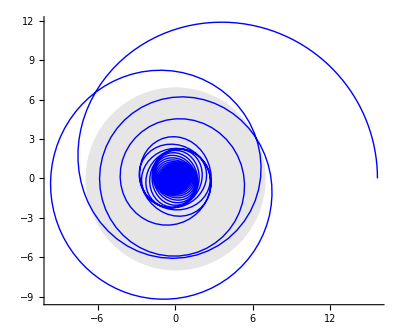

```mathematica
x[t_]:=rbarNumIn[t] Cos[phiNumIn[t]];
y[t_]:=rbarNumIn[t] Sin[phiNumIn[t]];
orbit2D=ParametricPlot[{x[t],y[t]},{t,t0,0.999 tFinish},AspectRatio->Automatic,AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Thick,Blue}];
(*Automatic scale makes the aces the same scale*)
centralBody=Graphics[{GrayLevel[0.9],Disk[{0,0},rbarStar]}];
Show[centralBody, orbit2D,AspectRatio->Automatic,PlotRange->All, Axes -> True]
```

```mathematica
FRRrFull[m_, rbar_, ur_, uphi_] := Piecewise[
{
{FRRr[m, rbar, ur, uphi], rbar >= rbarStar},
{FRRrIns[m, rbar, ur, uphi], rbar <rbarStar}
}
]
```

InterpolatingFunction::dmval: Input value {15.6507} lies outside the range of data in the interpolating function. Extrapolation will be used.

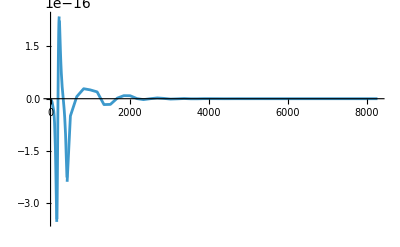

```mathematica
Plot[FRRrFull[massNumIn[t], rbarNumIn[t], urNumIn[t], uphiNumIn[t]], {t, 0, tFinish}, PlotRange->All]
```

```mathematica
FRRphiFull[m_, rbar_, ur_, uphi_] := Piecewise[
{
{FRRphi[m, rbar, ur, uphi], rbar >= rbarStar},
{FRRphiIns[m, rbar, ur, uphi], rbar <rbarStar}
}
]
```

InterpolatingFunction::dmval: Input value {15.6507} lies outside the range of data in the interpolating function. Extrapolation will be used.

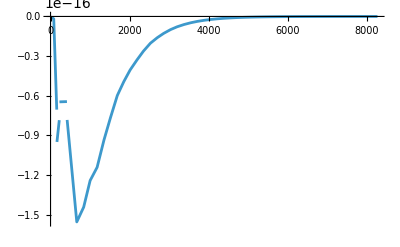

```mathematica
Plot[FRRphiFull[massNumIn[t], rbarNumIn[t], urNumIn[t], uphiNumIn[t]], {t, 0, tFinish}, PlotRange->All]
```

InterpolatingFunction::dmval: Input value {15.6507} lies outside the range of data in the interpolating function. Extrapolation will be used.

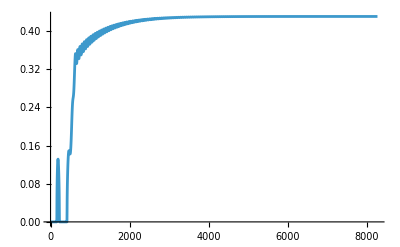

```mathematica
Plot[asosPiecewise[rbarNumIn[t]],{t,0,tFinish}, PlotRange->All]
```

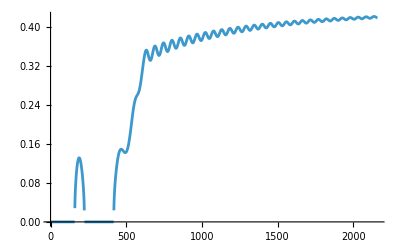

```mathematica
Plot[
{
Piecewise[
{
{0,rbarNumIn[t]>=rbarStar},
{asosPiecewise[rbarNumIn[t]],rbarNumIn[t]<rbarStar}
}
]
},
{t,0,tSurface+2000}, PlotRange->All
]
```

InterpolatingFunction::dmval: Input value {15.6507} lies outside the range of data in the interpolating function. Extrapolation will be used.

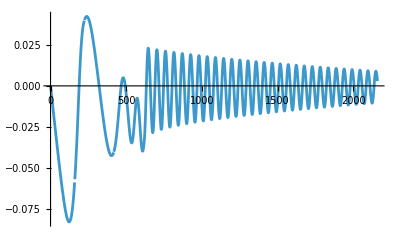

```mathematica
Plot[
{
Piecewise[
{
{drBardt[rbarNumIn[t],urNumIn[t],uphiNumIn[t]],rbarNumIn[t]>=rbarStar},
{drBardtInside[rbarNumIn[t],urNumIn[t],uphiNumIn[t]],rbarNumIn[t]<rbarStar}
}
]
},
{t,0,tSurface+2000}, PlotRange->All
]
```

InterpolatingFunction::dmval: Input value {15.6507} lies outside the range of data in the interpolating function. Extrapolation will be used.

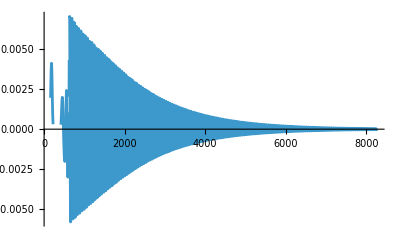

```mathematica
Plot[
{
Piecewise[
{
{durdt2DOutside[rbarNumIn[t],urNumIn[t],uphiNumIn[t]],rbarNumIn[t]>=rbarStar},
{durdt2DInside[massNumIn[t], rbarNumIn[t],urNumIn[t],uphiNumIn[t]],rbarNumIn[t]<rbarStar}
}
]
},
{t,0,tFinish}, PlotRange->All
]
```

InterpolatingFunction::dmval: Input value {15.6507} lies outside the range of data in the interpolating function. Extrapolation will be used.

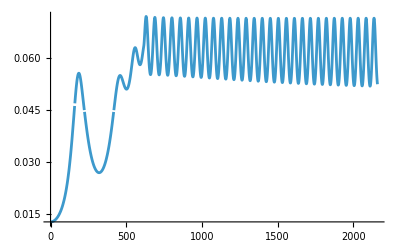

```mathematica
Plot[
{
Piecewise[
{
{dphidtOutside[rbarNumIn[t],urNumIn[t],uphiNumIn[t]],rbarNumIn[t]>=rbarStar},
{dphidtInside[rbarNumIn[t],urNumIn[t],uphiNumIn[t]],rbarNumIn[t]<rbarStar}
}
]
},
{t,0,tSurface+2000}, PlotRange->All
]
```

InterpolatingFunction::dmval: Input value {15.6507} lies outside the range of data in the interpolating function. Extrapolation will be used.

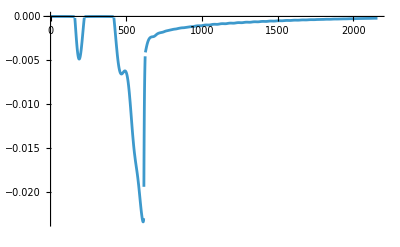

```mathematica
Plot[
{
Piecewise[
{
{duphidtOutside[massNumIn[t], rbarNumIn[t],urNumIn[t],uphiNumIn[t]], rbarNumIn[t]>=rbarStar},
{duphidtInside[massNumIn[t], rbarNumIn[t],urNumIn[t],uphiNumIn[t]],rbarNumIn[t]<rbarStar}
}
]
},
{t,0,tSurface+2000}, PlotRange->All
]
```

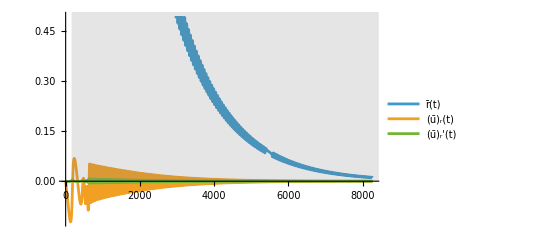

```mathematica
outFigRadial=Show[Plot[{rbarNumIn[t],urNumIn[t],urNumIn'[t]},{t,t0,.999 tFinish},PlotLegends->LineLegend[Automatic,{"r̄(t)","(ū)_r(t)","(ū)_r'(t)"}]],Plot[rbarStar,{t,tSurface,tSurface+tFinish},PlotStyle->Directive[Gray,Opacity[0.1]],Filling->Bottom]]
```

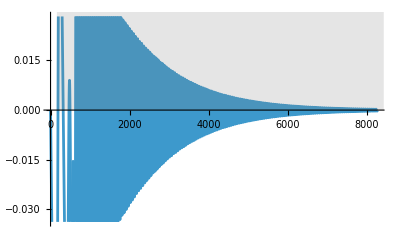

```mathematica
outFigRadial=Show[Plot[{urNumIn[t]},{t,t0, tFinish},PlotLegends->LineLegend[Automatic,{"r̄(t)","(ū)_r(t)","(ū)_r'(t)"}]],Plot[rbarStar,{t,tSurface,tSurface+tFinish},PlotStyle->Directive[Gray,Opacity[0.1]],Filling->Bottom]]
```

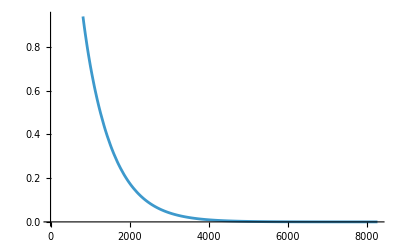

```mathematica
outFigAngular=Plot[{uphiNumIn[t]},{t,t0,tFinish},PlotLegends->LineLegend[Automatic,{"phi(t)","uphi(t)","uphi'(t)"}]]
```

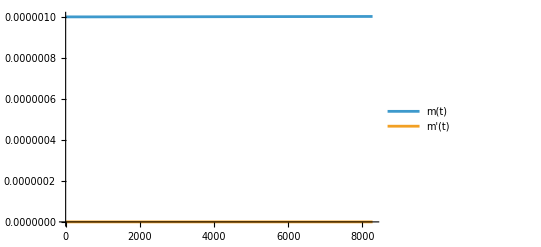

```mathematica
outFigMass=Show[Plot[{massNumIn[t],massNumIn'[t]},{t,t0,tFinish},PlotLegends->LineLegend[Automatic,{"m(t)","m'(t)"}]]]
```

```mathematica
umag[rbar_, ur_, uphi_] := Piecewise[
{
{umagOutside[rbar, ur, uphi], rbar >= rbarStar},
{umagInside[rbar, ur, uphi], rbar < rbarStar}
}
]
```

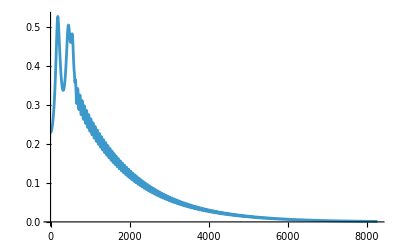

```mathematica
Plot[umag[rbarNumIn[t], urNumIn[t], uphiNumIn[t]], {t, 0, tFinish}, Exclusions->None] (*Normal behaviour judging from rho=const simulation*)
```

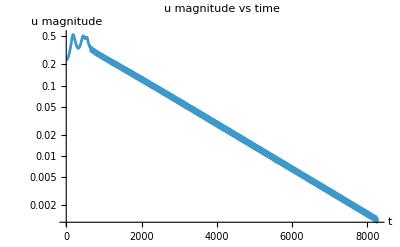

```mathematica
LogPlot[Evaluate[umag[rbarNumIn[t],urNumIn[t],uphiNumIn[t]]/. solIn],{t,0,tFinish},PlotRange->All,AxesLabel->{"t","u magnitude"},PlotLabel->"u magnitude vs time"]
```

```mathematica
(*Show me the value of u at tfinish*)
umag[rbarNumIn[tFinish],urNumIn[tFinish],uphiNumIn[tFinish]]/. solIn
```

0.00134193

## Gravitational-wave strains

### h_+

```mathematica
hplusInside[d_, m_, rbar_, ur_, uphi_, phi_] := Module[{r = rofrbarInside[rbar], rd, phid},
rd = drBardtInside[rbar,ur,uphi];
phid = dphidtInside[rbar,ur,uphi];
((-2m)/d)((MassFunc[r] Cos[2 phi])/r - rd^2 Cos[2phi] + 2rd r phid Sin[2phi] + (r phid)^2 Cos[2phi])
]
```

```mathematica
hplusOutside[d_, m_, rbar_, ur_, uphi_, phi_] := Module[{r = rofrbarOutside[rbar], rd, phid},
rd = drBardt[rbar,ur,uphi];
phid = dphidtOutside[rbar,ur,uphi];
((-2m)/d)((M Cos[2 phi])/r - rd^2 Cos[2phi] + 2rd r phid Sin[2phi] + (r phid)^2 Cos[2phi])
]
```

```mathematica
hplusFull[d_, m_, rbar_, ur_, uphi_,phi_] := Piecewise[
{
{hplusOutside[d, m, rbar, ur, uphi, phi], rbar >= rbarStar},
{hplusInside[d, m, rbar, ur, uphi, phi], rbar < rbarStar}
}
]
```

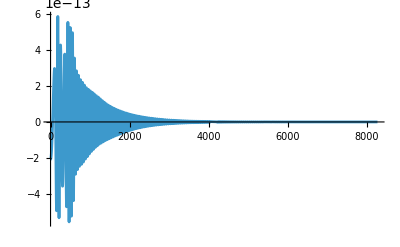

```mathematica
Plot[hplusFull[10^6, massNumIn[t], rbarNumIn[t], urNumIn[t], uphiNumIn[t], phiNumIn[t]], {t, 0, tFinish}, PlotRange->Full, Exclusions->None] (*10^8 it gets jagged*)
```

### h_x

```mathematica
hxInside[d_, m_, rbar_, ur_, uphi_, phi_] := Module[{r = rofrbarInside[rbar], rd, phid},
rd = drBardtInside[rbar,ur,uphi];
phid = dphidtInside[rbar,ur,uphi];
((-2m)/d)((MassFunc[r] Sin[2 phi])/r - 2(rd Sin[phi] + r phid Cos[phi])(rd Cos[phi] - r phid Sin[phi]))
]
```

```mathematica
hxOutside[d_, m_, rbar_, ur_, uphi_, phi_] := Module[{r = rofrbarOutside[rbar], rd, phid},
rd = drBardt[rbar,ur,uphi];
phid = dphidtOutside[rbar,ur,uphi];
((-2m)/d)((M Sin[2 phi])/r - 2(rd Sin[phi] + r phid Cos[phi])(rd Cos[phi] - r phid Sin[phi]))
]
```

```mathematica
hxFull[d_, m_, rbar_, ur_, uphi_,phi_] := Piecewise[
{
{hxOutside[d, m, rbar, ur, uphi, phi], rbar >= rbarStar},
{hxInside[d, m, rbar, ur, uphi, phi], rbar < rbarStar}
}
]
```

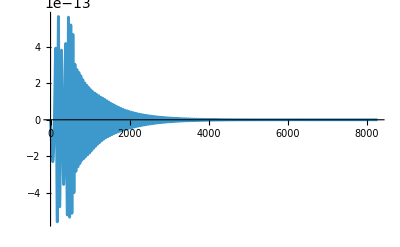

```mathematica
Plot[hxFull[10^6, massNumIn[t], rbarNumIn[t], urNumIn[t], uphiNumIn[t], phiNumIn[t]], {t, 0, tFinish}, PlotRange->Full, Exclusions->None] (*10^8 it gets jagged*)
```

## Energy loss during orbits CHECK angles and other assumptions made by authors for these formulae especially the angular momentum stuff.

### Instantaneous energy loss (coordinate system dependent)

```mathematica
dEdtInside[m_,rbar_,ur_,uphi_]:=Module[{r=rofrbarInside[rbar],rd,phid},rd=drBardtInside[rbar,ur,uphi];
phid=dphidtInside[rbar,ur,uphi];
(8 m^2)/(15 r^4)*(MassFunction[r]^2*(8 rd^2+6 (r phid)^2)+r MassFunction[r]*(6 rd^4-6 (3(r phid)^4+(r phid)^2 Mp[r])+rd^2 (63 (r phid)^2+Mp[r]-3 r Mpp[r]))+r^2*(6 (r phid)^4 Mp[r]-rd^2 ((Mp[r])^2+3 (r phid)^2 (13 Mp[r]-3 r Mpp[r]))-rd^4 (2 Mp[r]+r Mpp[r]-r^2 Mppp[r])))]
```

```mathematica
dEdtOutside[m_,rbar_,ur_,uphi_]:=Module[{r=rofrbarOutside[rbar],rd,phid},rd=drBardt[rbar,ur,uphi];
phid=dphidtOutside[rbar,ur,uphi];
(8 m^2)/(15 r^4)*(M^2*(8 rd^2+6 (r phid)^2)+r M*(6 rd^4-6 (3(r phid)^4)+rd^2 (63 (r phid)^2)))]
```

```mathematica
dEdtFull[m_, rbar_, ur_, uphi_] := Piecewise[
{
{dEdtOutside[m, rbar, ur, uphi], rbar >= rbarStar},
{dEdtInside[m, rbar, ur, uphi], rbar <rbarStar}
}
]
```

InterpolatingFunction::dmval: Input value {15.6507} lies outside the range of data in the interpolating function. Extrapolation will be used.

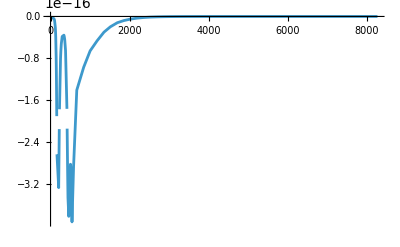

```mathematica
Plot[dEdtFull[massNumIn[t], rbarNumIn[t], urNumIn[t], uphiNumIn[t]], {t, 0, tFinish}, PlotRange->All]
```

### Average, physical energy loss per orbit N/A

```mathematica
dEdtAvg[m_,M_,a_,e_]:=-(32 m^2 M^3)/(5 a^5 (1-e^2)^(7/2))*(1+(73/24) e^2+(37/96) e^4)
```

Need formulae for M[t]? Although accretion is very small. a(t) and e(t)

## Angular momentum loss during orbits

### Instantaneous angular momentum loss (coordinate system dependent)

```mathematica
dLdtOutside[m_, rbar_, ur_, uphi_]:= Module[{r=rofrbarOutside[rbar]},
r^2 FRRphi[m, rbar, ur, uphi]]
dLdtInside[m_, rbar_, ur_, uphi_]:= Module[{r=rofrbarInside[rbar]},
r^2 FRRphiIns[m, rbar, ur, uphi]]
```

```mathematica
dLdtFull[m_, rbar_, ur_, uphi_] := Piecewise[
{
{dLdtOutside[m, rbar, ur, uphi], rbar >= rbarStar},
{dLdtInside[m, rbar, ur, uphi], rbar <rbarStar}
}
]
```

InterpolatingFunction::dmval: Input value {15.6507} lies outside the range of data in the interpolating function. Extrapolation will be used.

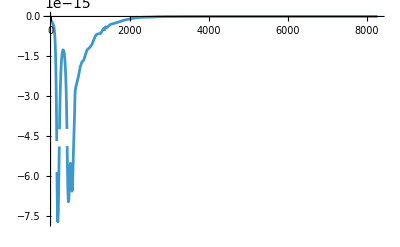

```mathematica
Plot[dLdtFull[massNumIn[t], rbarNumIn[t], urNumIn[t], uphiNumIn[t]], {t, 0, tFinish}, PlotRange->All]
```

### Average, physical angular momentum loss per orbit N/A

```mathematica
(*Formula might need to be adjusted for me as they use the angle phi = 0 for when it crosses the star surface which is not true for me*)
```

```mathematica
dLdtAvg[m_,M_,a_,e_]:=-(32 m^2 M^(5/2))/(5 a^(7/2) (1-e^2)^(2))*(1+(7/8) e^2)
```

Need formulae for M[t]? Although accretion is very small. a(t) and e(t).

Use E and L to find a(t) and e(t)??